```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LC EOP\\Vertical.xlsx"]
```

```mathematica
data3={{-75.,0.9595238095238094},{-70.,0.955116696588869},{-65.,0.9587786259541984},{-60.,0.963888888888889},{-55.,0.9893190921228303},{-50.,1.0542740841248304},{-45.,1.1676300578034682},{-40.,1.3559870550161812},{-35.,1.680232558139535},{-30.,2.211302211302211},{-25.,3.1496598639455784},{-20.,4.83248730964467},{-15.,8.193277310924369},{-10.,14.333333333333334},{-5.,22.68181818181818},{0.,21.73913043478261},{5.,14.014084507042254},{10.,8.5},{15.,5.348066298342541},{20.,3.6511627906976742},{25.,2.6217765042979946},{30.,1.9116379310344829},{35.,1.526126126126126},{40.,1.2515337423312882},{45.,1.0865921787709498},{50.,0.9946236559139784},{55.,0.9570451436388508},{60.,0.9531478770131772},{65.,0.9639934533551554},{70.,0.974559686888454},{75.,0.981578947368421}}
```

{{-75.,0.959524},{-70.,0.955117},{-65.,0.958779},{-60.,0.963889},{-55.,0.989319},{-50.,1.05427},{-45.,1.16763},{-40.,1.35599},{-35.,1.68023},{-30.,2.2113},{-25.,3.14966},{-20.,4.83249},{-15.,8.19328},{-10.,14.3333},{-5.,22.6818},{0.,21.7391},{5.,14.0141},{10.,8.5},{15.,5.34807},{20.,3.65116},{25.,2.62178},{30.,1.91164},{35.,1.52613},{40.,1.25153},{45.,1.08659},{50.,0.994624},{55.,0.957045},{60.,0.953148},{65.,0.963993},{70.,0.97456},{75.,0.981579}}

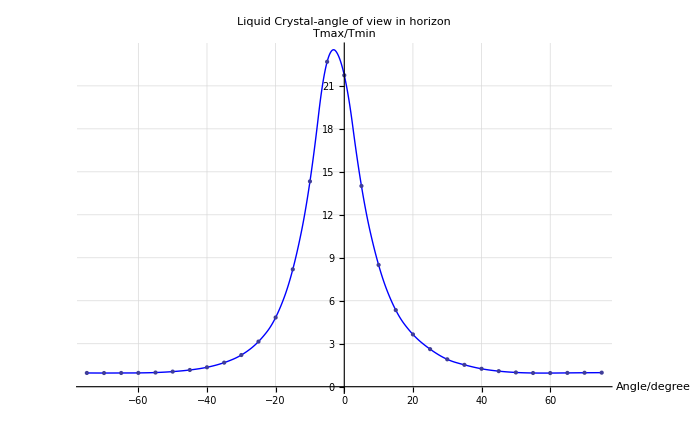

```mathematica
Show[gra1=ListLinePlot[data3,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/degree","Tmax/Tmin"},PlotLabel->"Liquid Crystal-angle of view in horizon",GridLines->Automatic],ListPlot[data3]]
```